## Shear Analysis

L: | 56.333
m: | 84
kappa: | 0.2
sigma: | 0.000267
kappa_sigma_r: | 749.906
Delta: | 0.333331
Extension Minimum: | 0
Extension Maximum: | 75
beta: | 4.
mu: | 0.31
c: | 0.8
delta: | 5.91
b: | 0.9
k: | 0.39
ev0: | 1.46
C0: | 0.36
e0: | 0.005001
beta: | 38.6817

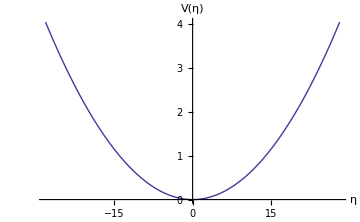

0.333331

Backbone spring constant κ:

0.2

Residue-pair spring constant σ(ϵ = 0.005001):

0.000267

κ/σ ratio:

749.906

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
Needs["PlotLegends`"]
<<Units`
<<PhysicalConstants`

PotentialData = Import["potential_data.out","Table"];

PartitionFunction=Import["PartitionFunction_0_0.out","Table"];
FreeEnergy=Import["FreeEnergy_0_0.out","Table"];
dPartitionFunction=Import["dPartitionFunction_0_0.out","Table"];
dFreeEnergy=Import["dFreeEnergy_0_0.out","Table"];

Subscript[R, pfmxd]=Import["pfmxd_r.out","Table"];
Subscript[R, mxd]=Import["mxd_r.out","Table"];

Subscript[λ, pfmxd]=Import["pfmxd_lambda.out","Table"];
Subscript[λ, mxd]=Import["mxd_lambda.out","Table"];

Subscript[ρ, pfmxd]=Import["pfmxd_roe.out","Table"];
Subscript[ρ, mxd]=Import["mxd_roe.out","Table"];

Parameters=Import["Parameters"];
Grid[Parameters]
Needs["PlotLegends`"]
PlotPotentialData=ListLinePlot[{PotentialData},ImageSize->Medium,AxesOrigin->{0,0},AxesLabel->{Style["η",FontSize->18],Style["V(η)",FontSize->18]},PlotStyle->Thick,PlotRange->All]

ϵ=Parameters[[17,2]];
β=Parameters[[18,2]];

L=Parameters[[1,2]];
m=Parameters[[2,2]];
Δ=Parameters[[6,2]]
Print["Backbone spring constant κ:"]
κ=Parameters[[3,2]]
Print["Residue-pair spring constant σ(ϵ = "<>ToString[ϵ]<>"):"]
σ=Parameters[[4,2]]
Print["κ/σ ratio:"]
κσr=Parameters[[5,2]]
umax=Parameters[[7,2]];
umax=Parameters[[8,2]];

n=ToExpression[StringTrim[Last[StringSplit[Directory[],"/"]],RegularExpression["N*"]]];

fsTitle=24;
fsAxesLabel=18;
fs2=16;

Subscript[η, B]=2.0;

ToNewton=Convert[ElectronVolt/Angstrom,Newton] SI[Pico Newton]^-1;(*Converts eV/Å to pN*)
ToForceDimension[f_]:=(f (κ/(2β))^(1/2)) ToNewton;
ToDimension[η_]:=η ((κ β)/2)^(-1/2)(*Converts to Å*)
```

### Length Dimension Check

```mathematica
Subscript[η, B] (*No Dimension*)
ToDimension[Subscript[η, B]](*Å*)
```

2.

1.0169

### Force Dimension Check

```mathematica
0.5 (*No Dimension*)
σ ToDimension[Subscript[η, B]] ToNewton  (*pN*)
ToForceDimension[0.5] (*Converts force to dimensions of eV/Å then to J/m for pN*)
```

0.5

0.43501

40.7313

Partition function & Free Energy

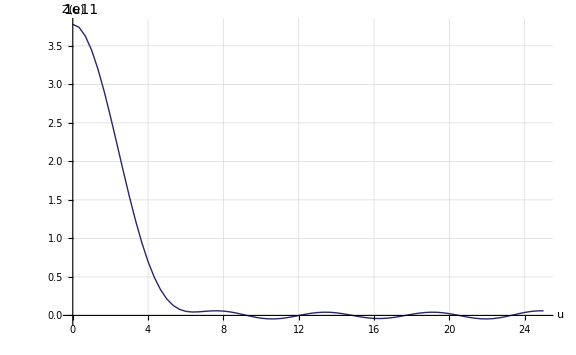
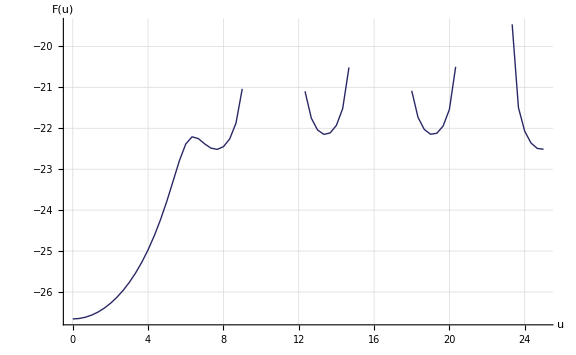

```mathematica
pIntactPF=ListLinePlot[PartitionFunction,ImageSize->Large,PlotStyle->{Thick,Darker[ColorData[1,1]]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["Z(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}];

pIntactFE=ListLinePlot[FreeEnergy,ImageSize->Large,PlotStyle->{Thick,Darker[ColorData[1,1]]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}];

{pIntactPF,pIntactFE}
```

Residue-pair separations (x-z), (x-y), (z-y)

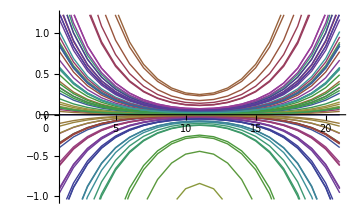
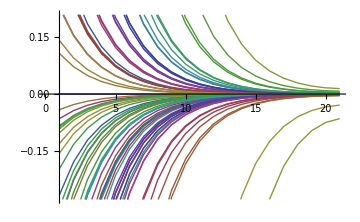

1.83954

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0644115 | 0.0435924 | 0.0295192 | 0.0200139 | 0.0136057 | 0.00930295 | 0.00643977 | 0.00457313 | 0.00341416 | 0.00278352 | 0.00258362 | 0.00278352 | 0.00341416 | 0.00457313 | 0.00643977 | 0.00930295 | 0.0136057 | 0.0200139 | 0.0295192 | 0.0435925 | 0.0644115
0.12946 | 0.0876159 | 0.0593302 | 0.0402257 | 0.0273459 | 0.0186979 | 0.0129432 | 0.00919147 | 0.00686207 | 0.00559456 | 0.00519277 | 0.00559456 | 0.00686207 | 0.00919147 | 0.0129432 | 0.0186979 | 0.0273459 | 0.0402257 | 0.0593302 | 0.0876159 | 0.12946
0.195808 | 0.132519 | 0.0897369 | 0.0608414 | 0.0413607 | 0.0282805 | 0.0195766 | 0.0139021 | 0.0103789 | 0.00846177 | 0.00785407 | 0.00846177 | 0.0103789 | 0.0139021 | 0.0195766 | 0.0282805 | 0.0413607 | 0.0608413 | 0.0897369 | 0.132519 | 0.195808
0.264173 | 0.178787 | 0.121068 | 0.0820839 | 0.0558017 | 0.0381545 | 0.0264117 | 0.018756 | 0.0140026 | 0.0114162 | 0.0105963 | 0.0114162 | 0.0140026 | 0.018756 | 0.0264117 | 0.0381545 | 0.0558017 | 0.0820839 | 0.121068 | 0.178787 | 0.264173
0.335361 | 0.226966 | 0.153693 | 0.104203 | 0.0708387 | 0.0484361 | 0.0335289 | 0.0238102 | 0.0177759 | 0.0144925 | 0.0134517 | 0.0144925 | 0.017776 | 0.0238102 | 0.0335289 | 0.0484361 | 0.0708387 | 0.104203 | 0.153693 | 0.226966 | 0.335361
0.4103 | 0.277683 | 0.188037 | 0.127488 | 0.0866682 | 0.0592596 | 0.0410213 | 0.0291308 | 0.0217482 | 0.017731 | 0.0164576 | 0.017731 | 0.0217482 | 0.0291308 | 0.0410213 | 0.0592596 | 0.0866682 | 0.127488 | 0.188037 | 0.277683 | 0.4103
0.490095 | 0.331687 | 0.224606 | 0.152282 | 0.103523 | 0.0707844 | 0.048999 | 0.0347961 | 0.0259777 | 0.0211793 | 0.0196583 | 0.0211793 | 0.0259777 | 0.0347961 | 0.048999 | 0.0707844 | 0.103523 | 0.152282 | 0.224606 | 0.331687 | 0.490095
0.576078 | 0.389879 | 0.264011 | 0.178999 | 0.121686 | 0.083203 | 0.0575955 | 0.0409008 | 0.0305353 | 0.024895 | 0.0231071 | 0.024895 | 0.0305353 | 0.0409008 | 0.0575955 | 0.083203 | 0.121686 | 0.178999 | 0.264011 | 0.389879 | 0.576078
0.66988 | 0.453362 | 0.307 | 0.208145 | 0.141499 | 0.0967507 | 0.0669737 | 0.0475606 | 0.0355073 | 0.0289486 | 0.0268696 | 0.0289486 | 0.0355073 | 0.0475606 | 0.0669737 | 0.0967507 | 0.1415 | 0.208145 | 0.307 | 0.453362 | 0.66988
0.773481 | 0.523477 | 0.35448 | 0.240336 | 0.163383 | 0.111714 | 0.0773316 | 0.0549162 | 0.0409987 | 0.0334257 | 0.0310252 | 0.0334257 | 0.0409987 | 0.0549162 | 0.0773316 | 0.111714 | 0.163383 | 0.240336 | 0.35448 | 0.523477 | 0.773481
0.88922 | 0.601807 | 0.407521 | 0.276298 | 0.187831 | 0.12843 | 0.088903 | 0.0631335 | 0.0471335 | 0.0384273 | 0.0356676 | 0.0384273 | 0.0471335 | 0.0631334 | 0.088903 | 0.12843 | 0.187831 | 0.276298 | 0.407521 | 0.601807 | 0.88922
1.01956 | 0.690022 | 0.467257 | 0.316799 | 0.215364 | 0.147256 | 0.101935 | 0.0723878 | 0.0540425 | 0.0440601 | 0.0408959 | 0.0440601 | 0.0540425 | 0.0723878 | 0.101935 | 0.147256 | 0.215364 | 0.316799 | 0.467257 | 0.690022 | 1.01956
1.16619 | 0.789253 | 0.534453 | 0.362357 | 0.246335 | 0.168432 | 0.116594 | 0.0827978 | 0.0618143 | 0.0503964 | 0.0467771 | 0.0503964 | 0.0618143 | 0.0827978 | 0.116594 | 0.168432 | 0.246335 | 0.362357 | 0.534453 | 0.789253 | 1.16619
1.32684 | 0.89798 | 0.608079 | 0.412276 | 0.28027 | 0.191635 | 0.132656 | 0.0942039 | 0.0703298 | 0.0573389 | 0.0532211 | 0.0573389 | 0.0703298 | 0.0942039 | 0.132656 | 0.191636 | 0.28027 | 0.412275 | 0.608079 | 0.89798 | 1.32684
1.48572 | 1.0055 | 0.68089 | 0.461641 | 0.31383 | 0.214582 | 0.14854 | 0.105484 | 0.0787511 | 0.0642047 | 0.0595937 | 0.0642047 | 0.0787511 | 0.105484 | 0.14854 | 0.214582 | 0.31383 | 0.461641 | 0.68089 | 1.0055 | 1.48572
1.58651 | 1.07372 | 0.727084 | 0.49296 | 0.335121 | 0.22914 | 0.158617 | 0.11264 | 0.0840938 | 0.0685605 | 0.0636367 | 0.0685605 | 0.0840938 | 0.11264 | 0.158617 | 0.22914 | 0.335121 | 0.49296 | 0.727084 | 1.07372 | 1.58651
1.47992 | 1.00158 | 0.678232 | 0.459839 | 0.312604 | 0.213744 | 0.14796 | 0.105072 | 0.0784436 | 0.063954 | 0.0593611 | 0.063954 | 0.0784436 | 0.105072 | 0.14796 | 0.213744 | 0.312604 | 0.459839 | 0.678232 | 1.00158 | 1.47991
0.954174 | 0.645767 | 0.437289 | 0.296481 | 0.201551 | 0.137811 | 0.095397 | 0.0677451 | 0.0505764 | 0.0412343 | 0.038273 | 0.0412343 | 0.0505764 | 0.0677451 | 0.095397 | 0.137811 | 0.201551 | 0.296481 | 0.437289 | 0.645767 | 0.954174
0.154804 | 0.104768 | 0.0709451 | 0.0481005 | 0.0326994 | 0.0223583 | 0.0154771 | 0.0109908 | 0.00820544 | 0.00668978 | 0.00620935 | 0.00668978 | 0.00820544 | 0.0109908 | 0.015477 | 0.0223583 | 0.0326993 | 0.0481005 | 0.0709451 | 0.104768 | 0.154804
-0.342895 | -0.232065 | -0.157146 | -0.106544 | -0.0724302 | -0.0495244 | -0.0342822 | -0.0243451 | -0.0181753 | -0.0148181 | -0.0137539 | -0.0148181 | -0.0181753 | -0.0243451 | -0.0342822 | -0.0495244 | -0.0724302 | -0.106544 | -0.157146 | -0.232065 | -0.342895
-0.402043 | -0.272095 | -0.184253 | -0.124923 | -0.084924 | -0.058067 | -0.0401957 | -0.0285445 | -0.0213105 | -0.0173741 | -0.0161264 | -0.0173741 | -0.0213105 | -0.0285445 | -0.0401957 | -0.058067 | -0.084924 | -0.124923 | -0.184253 | -0.272095 | -0.402043
-0.229374 | -0.155236 | -0.10512 | -0.071271 | -0.0484509 | -0.0331285 | -0.0229325 | -0.0162852 | -0.0121581 | -0.00991231 | -0.00920044 | -0.00991231 | -0.0121581 | -0.0162852 | -0.0229325 | -0.0331285 | -0.0484509 | -0.071271 | -0.10512 | -0.155236 | -0.229374
0.0408752 | 0.0276635 | 0.0187327 | 0.0127007 | 0.00863411 | 0.0059036 | 0.00408664 | 0.00290208 | 0.00216661 | 0.00176641 | 0.00163955 | 0.00176641 | 0.00216661 | 0.00290208 | 0.00408664 | 0.0059036 | 0.00863411 | 0.0127007 | 0.0187327 | 0.0276635 | 0.0408752
0.381332 | 0.258078 | 0.174761 | 0.118488 | 0.0805493 | 0.0550758 | 0.0381251 | 0.0270741 | 0.0202127 | 0.0164791 | 0.0152957 | 0.0164792 | 0.0202127 | 0.0270741 | 0.0381251 | 0.0550758 | 0.0805493 | 0.118488 | 0.174761 | 0.258079 | 0.381333
0.845691 | 0.572347 | 0.387572 | 0.262773 | 0.178636 | 0.122143 | 0.0845511 | 0.0600429 | 0.0448262 | 0.0365462 | 0.0339216 | 0.0365462 | 0.0448263 | 0.0600429 | 0.0845511 | 0.122143 | 0.178636 | 0.262773 | 0.387572 | 0.572347 | 0.845691
1.66112 | 1.12421 | 0.761274 | 0.516141 | 0.350879 | 0.239915 | 0.166076 | 0.117937 | 0.0880482 | 0.0717845 | 0.0666292 | 0.0717845 | 0.0880482 | 0.117937 | 0.166076 | 0.239915 | 0.350879 | 0.516141 | 0.761274 | 1.12421 | 1.66112
4.32504 | 2.92711 | 1.98213 | 1.34388 | 0.913585 | 0.624666 | 0.432412 | 0.307072 | 0.229251 | 0.186905 | 0.173482 | 0.186905 | 0.229251 | 0.307072 | 0.432412 | 0.624666 | 0.913585 | 1.34388 | 1.98213 | 2.92711 | 4.32505
-11.1757 | -7.56351 | -5.12173 | -3.47251 | -2.36066 | -1.61411 | -1.11733 | -0.793461 | -0.592374 | -0.482955 | -0.448271 | -0.482955 | -0.592374 | -0.793461 | -1.11733 | -1.61411 | -2.36066 | -3.47251 | -5.12173 | -7.56351 | -11.1757
-2.19288 | -1.4841 | -1.00498 | -0.68137 | -0.463204 | -0.316717 | -0.219241 | -0.155691 | -0.116235 | -0.0947644 | -0.0879588 | -0.0947644 | -0.116235 | -0.155691 | -0.219241 | -0.316717 | -0.463204 | -0.68137 | -1.00498 | -1.4841 | -2.19288
-0.957186 | -0.647805 | -0.43867 | -0.297417 | -0.202188 | -0.138246 | -0.0956982 | -0.067959 | -0.0507361 | -0.0413645 | -0.0383938 | -0.0413645 | -0.0507361 | -0.067959 | -0.0956982 | -0.138246 | -0.202188 | -0.297417 | -0.43867 | -0.647805 | -0.957186
-0.353712 | -0.239385 | -0.162103 | -0.109905 | -0.074715 | -0.0510866 | -0.0353636 | -0.0251131 | -0.0187487 | -0.0152855 | -0.0141878 | -0.0152855 | -0.0187487 | -0.0251131 | -0.0353636 | -0.0510866 | -0.074715 | -0.109905 | -0.162103 | -0.239385 | -0.353712
0.101789 | 0.0688888 | 0.046649 | 0.0316278 | 0.021501 | 0.0147014 | 0.0101767 | 0.00722688 | 0.00539537 | 0.00439877 | 0.00408287 | 0.00439877 | 0.00539537 | 0.00722688 | 0.0101767 | 0.0147014 | 0.021501 | 0.0316278 | 0.046649 | 0.0688888 | 0.101789
0.571506 | 0.386784 | 0.261916 | 0.177578 | 0.12072 | 0.0825426 | 0.0571384 | 0.0405762 | 0.030293 | 0.0246974 | 0.0229237 | 0.0246974 | 0.0302929 | 0.0405762 | 0.0571384 | 0.0825426 | 0.12072 | 0.177578 | 0.261916 | 0.386784 | 0.571506
1.2408 | 0.839752 | 0.568649 | 0.385542 | 0.262097 | 0.179209 | 0.124054 | 0.0880955 | 0.0657694 | 0.0536209 | 0.0497701 | 0.0536209 | 0.0657694 | 0.0880955 | 0.124054 | 0.179209 | 0.262097 | 0.385542 | 0.568649 | 0.839753 | 1.2408
2.80653 | 1.89941 | 1.28621 | 0.872044 | 0.592827 | 0.405347 | 0.280593 | 0.19926 | 0.148761 | 0.121283 | 0.112573 | 0.121283 | 0.148761 | 0.19926 | 0.280593 | 0.405347 | 0.592827 | 0.872044 | 1.28621 | 1.89941 | 2.80653
43.1112 | 29.1768 | 19.7575 | 13.3955 | 9.10643 | 6.22655 | 4.3102 | 3.06084 | 2.28513 | 1.86304 | 1.72924 | 1.86304 | 2.28513 | 3.06084 | 4.3102 | 6.22655 | 9.10643 | 13.3955 | 19.7575 | 29.1768 | 43.1112
-3.21597 | -2.17651 | -1.47385 | -0.999265 | -0.679313 | -0.464482 | -0.321528 | -0.228329 | -0.170464 | -0.138977 | -0.128996 | -0.138977 | -0.170464 | -0.228329 | -0.321528 | -0.464482 | -0.679313 | -0.999265 | -1.47385 | -2.17651 | -3.21597
-1.30894 | -0.885866 | -0.599875 | -0.406714 | -0.276489 | -0.18905 | -0.130866 | -0.092933 | -0.069381 | -0.0565654 | -0.0525031 | -0.0565654 | -0.069381 | -0.092933 | -0.130866 | -0.18905 | -0.276489 | -0.406713 | -0.599875 | -0.885866 | -1.30894
-0.583732 | -0.395059 | -0.267519 | -0.181377 | -0.123302 | -0.0843084 | -0.0583607 | -0.0414442 | -0.030941 | -0.0252258 | -0.0234141 | -0.0252258 | -0.030941 | -0.0414442 | -0.0583607 | -0.0843084 | -0.123302 | -0.181377 | -0.267519 | -0.395059 | -0.583732
-0.106245 | -0.0719047 | -0.0486912 | -0.0330125 | -0.0224423 | -0.015345 | -0.0106222 | -0.00754326 | -0.00563157 | -0.00459134 | -0.00426161 | -0.00459134 | -0.00563157 | -0.00754326 | -0.0106222 | -0.015345 | -0.0224423 | -0.0330124 | -0.0486912 | -0.0719047 | -0.106245
0.330239 | 0.223499 | 0.151346 | 0.102612 | 0.0697568 | 0.0476964 | 0.0330168 | 0.0234465 | 0.0175045 | 0.0142712 | 0.0132463 | 0.0142712 | 0.0175045 | 0.0234465 | 0.0330169 | 0.0476964 | 0.0697568 | 0.102612 | 0.151346 | 0.223499 | 0.330239
0.866905 | 0.586705 | 0.397295 | 0.269364 | 0.183117 | 0.125207 | 0.086672 | 0.0615491 | 0.0459507 | 0.037463 | 0.0347725 | 0.037463 | 0.0459507 | 0.0615491 | 0.086672 | 0.125207 | 0.183117 | 0.269364 | 0.397295 | 0.586705 | 0.866905
1.82917 | 1.23794 | 0.83829 | 0.568358 | 0.386377 | 0.264186 | 0.182878 | 0.129868 | 0.0969558 | 0.0790468 | 0.0733699 | 0.0790468 | 0.0969558 | 0.129868 | 0.182878 | 0.264186 | 0.386377 | 0.568358 | 0.83829 | 1.23794 | 1.82917
5.75411 | 3.89427 | 2.63706 | 1.78792 | 1.21545 | 0.831066 | 0.575288 | 0.408534 | 0.304999 | 0.248662 | 0.230804 | 0.248662 | 0.304999 | 0.408534 | 0.575288 | 0.831066 | 1.21545 | 1.78792 | 2.63706 | 3.89427 | 5.75411
-6.73676 | -4.55931 | -3.08739 | -2.09324 | -1.42301 | -0.97299 | -0.673532 | -0.478301 | -0.357085 | -0.291127 | -0.270219 | -0.291127 | -0.357085 | -0.478301 | -0.673532 | -0.97299 | -1.42301 | -2.09324 | -3.0874 | -4.55931 | -6.73676
-1.92746 | -1.30447 | -0.883339 | -0.598901 | -0.407141 | -0.278384 | -0.192705 | -0.136847 | -0.102166 | -0.0832947 | -0.0773128 | -0.0832947 | -0.102166 | -0.136847 | -0.192705 | -0.278384 | -0.407141 | -0.598901 | -0.883339 | -1.30447 | -1.92746
-0.897003 | -0.607074 | -0.411088 | -0.278717 | -0.189475 | -0.129554 | -0.0896811 | -0.063686 | -0.0475461 | -0.0387637 | -0.0359798 | -0.0387637 | -0.047546 | -0.063686 | -0.0896811 | -0.129554 | -0.189475 | -0.278716 | -0.411088 | -0.607074 | -0.897003
-0.345107 | -0.233562 | -0.158159 | -0.107231 | -0.0728973 | -0.0498438 | -0.0345033 | -0.0245021 | -0.0182925 | -0.0149137 | -0.0138426 | -0.0149137 | -0.0182925 | -0.0245021 | -0.0345033 | -0.0498438 | -0.0728973 | -0.107231 | -0.158159 | -0.233562 | -0.345107
0.0914185 | 0.0618703 | 0.0418963 | 0.0284055 | 0.0193104 | 0.0132036 | 0.0091399 | 0.00649059 | 0.00484568 | 0.00395062 | 0.0036669 | 0.00395062 | 0.00484568 | 0.00649059 | 0.0091399 | 0.0132036 | 0.0193104 | 0.0284055 | 0.0418963 | 0.0618703 | 0.0914185
0.555822 | 0.37617 | 0.254728 | 0.172705 | 0.117407 | 0.0802773 | 0.0555703 | 0.0394626 | 0.0294616 | 0.0240196 | 0.0222946 | 0.0240196 | 0.0294616 | 0.0394626 | 0.0555703 | 0.0802773 | 0.117407 | 0.172705 | 0.254728 | 0.37617 | 0.555822
1.23496 | 0.835799 | 0.565972 | 0.383727 | 0.260863 | 0.178366 | 0.12347 | 0.0876808 | 0.0654598 | 0.0533685 | 0.0495358 | 0.0533685 | 0.0654598 | 0.0876807 | 0.12347 | 0.178366 | 0.260863 | 0.383727 | 0.565972 | 0.835799 | 1.23496
2.88024 | 1.94929 | 1.31999 | 0.894949 | 0.608398 | 0.415994 | 0.287963 | 0.204494 | 0.152669 | 0.124469 | 0.11553 | 0.124469 | 0.152669 | 0.204494 | 0.287963 | 0.415994 | 0.608398 | 0.894949 | 1.31999 | 1.94929 | 2.88024
95.6679 | 64.7462 | 43.8437 | 29.7259 | 20.208 | 13.8173 | 9.56475 | 6.79229 | 5.07092 | 4.13425 | 3.83735 | 4.13425 | 5.07092 | 6.79229 | 9.56475 | 13.8173 | 20.208 | 29.7259 | 43.8437 | 64.7462 | 95.6679
-3.1195 | -2.11122 | -1.42964 | -0.969289 | -0.658935 | -0.450549 | -0.311883 | -0.22148 | -0.16535 | -0.134808 | -0.125127 | -0.134808 | -0.16535 | -0.22148 | -0.311883 | -0.450549 | -0.658935 | -0.969289 | -1.42964 | -2.11122 | -3.1195
-1.31999 | -0.893343 | -0.604939 | -0.410147 | -0.278823 | -0.190646 | -0.131971 | -0.0937175 | -0.0699666 | -0.0570429 | -0.0529463 | -0.0570429 | -0.0699666 | -0.0937175 | -0.131971 | -0.190646 | -0.278823 | -0.410147 | -0.604939 | -0.893343 | -1.31999
-0.613047 | -0.414898 | -0.280954 | -0.190486 | -0.129495 | -0.0885423 | -0.0612916 | -0.0435255 | -0.0324948 | -0.0264926 | -0.02459 | -0.0264926 | -0.0324948 | -0.0435255 | -0.0612916 | -0.0885423 | -0.129495 | -0.190486 | -0.280954 | -0.414898 | -0.613047
-0.140254 | -0.0949212 | -0.0642771 | -0.0435797 | -0.029626 | -0.0202569 | -0.0140224 | -0.00995784 | -0.00743423 | -0.00606102 | -0.00562574 | -0.00606102 | -0.00743422 | -0.00995784 | -0.0140224 | -0.0202569 | -0.029626 | -0.0435797 | -0.0642771 | -0.0949212 | -0.140254
0.297378 | 0.20126 | 0.136286 | 0.0924013 | 0.0628156 | 0.0429503 | 0.0297315 | 0.0211135 | 0.0157627 | 0.0128511 | 0.0119282 | 0.0128511 | 0.0157627 | 0.0211135 | 0.0297315 | 0.0429503 | 0.0628156 | 0.0924013 | 0.136286 | 0.20126 | 0.297378
0.842616 | 0.570266 | 0.386163 | 0.261817 | 0.177987 | 0.121699 | 0.0842436 | 0.0598246 | 0.0446632 | 0.0364133 | 0.0337983 | 0.0364133 | 0.0446632 | 0.0598246 | 0.0842436 | 0.121699 | 0.177987 | 0.261817 | 0.386163 | 0.570266 | 0.842616
1.83954 | 1.24496 | 0.843043 | 0.57158 | 0.388567 | 0.265684 | 0.183914 | 0.130605 | 0.0975054 | 0.0794949 | 0.0737859 | 0.0794949 | 0.0975055 | 0.130605 | 0.183914 | 0.265684 | 0.388567 | 0.57158 | 0.843042 | 1.24496 | 1.83954
6.17749 | 4.1808 | 2.83109 | 1.91947 | 1.30488 | 0.892214 | 0.617617 | 0.438593 | 0.327441 | 0.266958 | 0.247786 | 0.266958 | 0.327441 | 0.438593 | 0.617617 | 0.892214 | 1.30488 | 1.91947 | 2.83108 | 4.1808 | 6.17749
-6.23311 | -4.21845 | -2.85658 | -1.93675 | -1.31663 | -0.900248 | -0.623178 | -0.442543 | -0.330389 | -0.269362 | -0.250017 | -0.269362 | -0.330389 | -0.442543 | -0.623178 | -0.900248 | -1.31663 | -1.93675 | -2.85658 | -4.21845 | -6.23311
-1.90833 | -1.29152 | -0.874569 | -0.592955 | -0.403099 | -0.27562 | -0.190792 | -0.135489 | -0.101152 | -0.0824677 | -0.0765452 | -0.0824677 | -0.101152 | -0.135489 | -0.190792 | -0.27562 | -0.403098 | -0.592955 | -0.874569 | -1.29152 | -1.90833
-0.909852 | -0.61577 | -0.416977 | -0.282709 | -0.192189 | -0.13141 | -0.0909658 | -0.0645983 | -0.0482271 | -0.0393189 | -0.0364952 | -0.0393189 | -0.0482271 | -0.0645983 | -0.0909658 | -0.13141 | -0.192189 | -0.282709 | -0.416977 | -0.61577 | -0.909852
-0.359911 | -0.243581 | -0.164944 | -0.111832 | -0.0760245 | -0.051982 | -0.0359835 | -0.0255532 | -0.0190773 | -0.0155534 | -0.0144365 | -0.0155534 | -0.0190773 | -0.0255532 | -0.0359835 | -0.051982 | -0.0760245 | -0.111832 | -0.164944 | -0.243581 | -0.359911
0.087031 | 0.0589009 | 0.0398855 | 0.0270423 | 0.0183837 | 0.0125699 | 0.00870125 | 0.00617909 | 0.00461312 | 0.00376102 | 0.00349091 | 0.00376102 | 0.00461312 | 0.00617909 | 0.00870125 | 0.0125699 | 0.0183837 | 0.0270423 | 0.0398855 | 0.0589009 | 0.087031
0.580035 | 0.392557 | 0.265825 | 0.180228 | 0.122522 | 0.0837744 | 0.0579911 | 0.0411817 | 0.030745 | 0.025066 | 0.0232659 | 0.025066 | 0.030745 | 0.0411817 | 0.0579911 | 0.0837744 | 0.122522 | 0.180228 | 0.265825 | 0.392557 | 0.580035
1.34543 | 0.910558 | 0.616596 | 0.41805 | 0.284196 | 0.19432 | 0.134514 | 0.0955234 | 0.0713149 | 0.0581421 | 0.0539665 | 0.0581421 | 0.0713149 | 0.0955234 | 0.134514 | 0.19432 | 0.284196 | 0.41805 | 0.616596 | 0.910558 | 1.34543
3.4917 | 2.36312 | 1.60022 | 1.08494 | 0.737557 | 0.504306 | 0.349096 | 0.247906 | 0.185079 | 0.150893 | 0.140056 | 0.150893 | 0.185079 | 0.247906 | 0.349096 | 0.504307 | 0.737557 | 1.08494 | 1.60022 | 2.36312 | 3.4917
-20.9897 | -14.2054 | -9.61939 | -6.52191 | -4.43368 | -3.03154 | -2.09852 | -1.49024 | -1.11257 | -0.907063 | -0.841921 | -0.907063 | -1.11257 | -1.49024 | -2.09852 | -3.03154 | -4.43368 | -6.52191 | -9.61939 | -14.2054 | -20.9897
-2.64862 | -1.79254 | -1.21384 | -0.822979 | -0.559472 | -0.38254 | -0.264806 | -0.188049 | -0.140391 | -0.114459 | -0.106239 | -0.114459 | -0.140392 | -0.188049 | -0.264806 | -0.38254 | -0.559472 | -0.822979 | -1.21384 | -1.79254 | -2.64862
-1.23697 | -0.837154 | -0.56689 | -0.384349 | -0.261286 | -0.178655 | -0.12367 | -0.0878229 | -0.0655659 | -0.053455 | -0.0496161 | -0.053455 | -0.0655659 | -0.0878229 | -0.12367 | -0.178655 | -0.261286 | -0.38435 | -0.56689 | -0.837154 | -1.23696
-0.624102 | -0.422381 | -0.286021 | -0.193921 | -0.13183 | -0.0901391 | -0.062397 | -0.0443105 | -0.0330808 | -0.0269704 | -0.0250335 | -0.0269704 | -0.0330808 | -0.0443105 | -0.0623969 | -0.0901391 | -0.13183 | -0.193921 | -0.286021 | -0.422381 | -0.624103
-0.225654 | -0.152718 | -0.103415 | -0.0701152 | -0.0476652 | -0.0325912 | -0.0225606 | -0.0160212 | -0.0119609 | -0.00975157 | -0.00905125 | -0.00975157 | -0.0119609 | -0.0160212 | -0.0225606 | -0.0325912 | -0.0476652 | -0.0701152 | -0.103415 | -0.152719 | -0.225654
0.0830435 | 0.0562023 | 0.0380581 | 0.0258033 | 0.0175414 | 0.011994 | 0.00830258 | 0.00589598 | 0.00440176 | 0.0035887 | 0.00333097 | 0.0035887 | 0.00440176 | 0.00589598 | 0.00830258 | 0.011994 | 0.0175414 | 0.0258033 | 0.0380581 | 0.0562023 | 0.0830435

Extension U (End base-pair separations at η_B) = 60

Extension U in terms of η = 19.9999 (60Δ)

```mathematica
xzpair=-(√3 Subscript[λ, mxd]+Subscript[ρ, mxd])/(√2);
xypair=√2 Subscript[ρ, mxd];

{ListLinePlot[xzpair,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}],ListLinePlot[xypair,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}]}
NearestValue=Nearest[Transpose[Chop[xzpair,10^-5]][[1]],Subscript[η, B]][[1]]
upos=Flatten[Position[Transpose[Chop[xzpair,10^-5]][[1]],NearestValue]][[1]];
U=upos-1;
Grid[Chop[xzpair,10^-5],Background->{Automatic,{upos->Yellow}}]
Print["Extension U (End base-pair separations at \!\(\*SubscriptBox[\"η\", \"B\"]\)) = ",U]
Print["Extension U in terms of η = ",U Δ," (",U,"Δ)"]
```

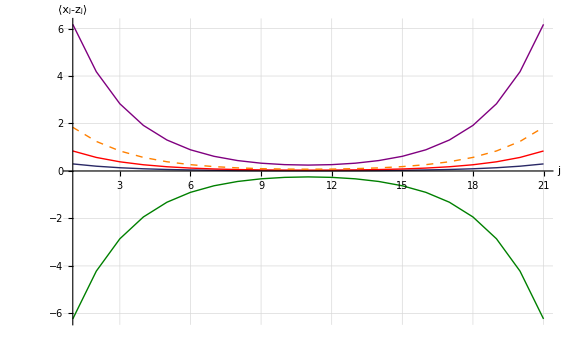
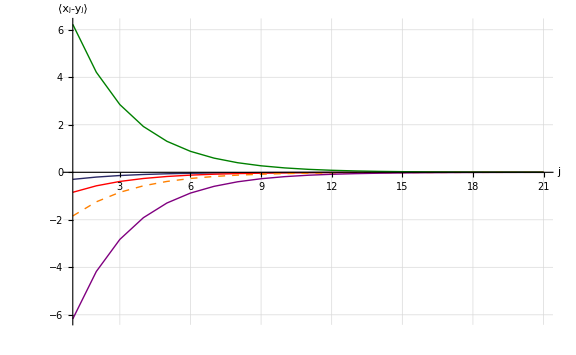

```mathematica
pos1=upos-2;
pos2=upos-1;
pos3=upos;
pos4=upos+1;
pos5=upos+2;

pxzpair=ListLinePlot[{xzpair[[pos1]],xzpair[[pos2]],xzpair[[pos3]],xzpair[[pos4]],xzpair[[pos5]]},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red},{Thick,Dashed,Orange},{Thick,Purple},{Thick,Darker[Green,0.5]}},PlotLegend->{Style["u="<>ToString[(pos1-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos2-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos3-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos4-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos5-1) Δ],FontSize->fs2]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],PlotRange->All,AxesOrigin->{1,0},AxesLabel->{Style["j",FontSize->fsAxesLabel],Style["⟨x_j-z_j⟩",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.55,LegendPosition->{0.9,-.2}];

pxypair=ListLinePlot[{xypair[[pos1]],xypair[[pos2]],xypair[[pos3]],xypair[[pos4]],xypair[[pos5]]},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red},{Thick,Dashed,Orange},{Thick,Purple},{Thick,Darker[Green,0.5]}},PlotLegend->{Style["u="<>ToString[(pos1-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos2-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos3-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos4-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos5-1) Δ],FontSize->fs2]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],PlotRange->All,AxesOrigin->{1,0},AxesLabel->{Style["j",FontSize->fsAxesLabel],Style["⟨x_j-y_j⟩",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.55,LegendPosition->{0.9,-.2}];

{pxzpair,pxypair}
```

Analysis

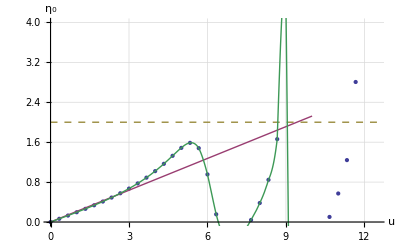

Interpolated Extension = 9.41788

```mathematica
y[x_]:=Subscript[η, B]
MXDp1=Plot[y[x],{x,0,umax Δ/2},PlotStyle->{ColorData[1,3],Dashed}];

MeanAxialDispDataRAW=Flatten[Transpose[Take[Transpose[xzpair],1]]];
maximumValue=Max[MeanAxialDispDataRAW];
positionOfMaximumValue=Flatten[Position[MeanAxialDispDataRAW,maximumValue]][[1]];

MeanAxialDispData = Table[{(i-1)Δ,MeanAxialDispDataRAW[[i]]},{i,1,positionOfMaximumValue}];
MXDp2=ListPlot[MeanAxialDispData];

model=a x  ;
MXDpara=FindFit[Take[MeanAxialDispData,10],model,{a},x];
mxd[u_]:=a u /.MXDpara
MXDp3=Plot[mxd[u],{u,0,10},PlotStyle->{ColorData[1,2]}];

mxdInterFunc=Interpolation[MeanAxialDispData];
u=u0/.Quiet[FindRoot[mxd[u0]==Subscript[η, B],{u0,0}]];

MXDp4=Plot[mxdInterFunc[x],{x,0,u+1},PlotStyle->ColorData[1,4]];

Show[{MXDp1,MXDp2,MXDp3,MXDp4},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["η_0",FontSize->fsAxesLabel]}]
Print["Interpolated Extension = ",u,"\n"]
```

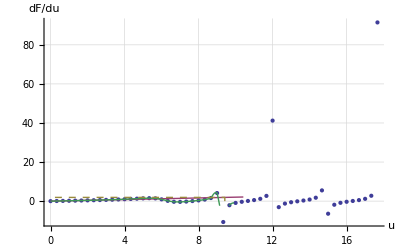

Interpolated Force = 1.91186

```mathematica
FreeEnergyMax=Max[Transpose[dFreeEnergy][[2]]];
positionOfFreeEnergyMax=Flatten[Position[dFreeEnergy,FreeEnergyMax]][[1]];
FreeEnergyData=Table[dFreeEnergy[[i]],{i,1,positionOfFreeEnergyMax}];
FEp1=ListPlot[FreeEnergyData];

model=a x  ;
FEpara=FindFit[Take[FreeEnergyData,10],model,{a},x];
dfe[u0_]:=a u0 /.FEpara
FEp2=Plot[dfe[u0],{u0,0,u+1},PlotStyle->{ColorData[1,2]}];

dfeInterFunc=Interpolation[FreeEnergyData];
F=dfe[u];


FEp3=Plot[dfeInterFunc[x],{x,0,u+.5},PlotStyle->ColorData[1,4]];


fpos={{u,0},{u,F},{0,F}};
FEp4=ListLinePlot[fpos,PlotStyle->{ColorData[1,3],Dashed}];

Show[{FEp1,FEp2,FEp3,FEp4},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["dF/du",FontSize->fsAxesLabel]}]
Print["Interpolated Force = ",F,"\n"]
```

### Force-Extension

```mathematica
Fc=ToForceDimension[F];
U=ToDimension[u];

Print["\nDimensional Force = ",Fc pN,"\nDimensional Extension = ",U Å,"\n"]
Export["N"<>ToString[n]<>"_sim.data",{{n,Fc}},"Table"];
```

Dimensional Force = 155.745 pN
Dimensional Extension = 4.78851 Å